```mathematica
q[t_,T0_,H_,m_,ω_]:=√((2H)/(m*ω^2))Cos[ω(t+T0)];
p[t_,T0_,H_,m_,ω_]:=-√(2H*ω)Sin[ω(t+T0)];
qdot[t_,T0_,H_,m_,ω_]:=p[t,T0,H,m,ω]/m;
pdot[t_,T0_,H_,m_,ω_]:=-ω*√(2H*ω)Cos[ω(t+T0)];
```

```mathematica
Manipulate[Show[ParametricPlot[{q[t,T0,H,1,2],p[t,T0,H,1,2]},{t,0,2Pi},PlotRange->{{-2,2},{-2,2}}],Graphics[{Red,PointSize[Large],Point[{q[0,T0,H,1,2],p[0,T0,H,1,2]}],Arrow[{{q[0,T0,H,1,2],p[0,T0,H,1,2]},{q[0,T0,H,1,2]+qdot[0,T0,H,1,2],p[0,T0,H,1,2]+pdot[0,T0,H,1,2]}}]}]],{T0,0,Pi},{H,0,1}]
```

### Energy re-parametrizations

```mathematica
φ[H_]:=H^2/2
ψ[T0_,H_]:=T0/H
```

```mathematica
Manipulate[Show[ParametricPlot[{q[t,ψ[T0,H],φ[H],1,2],p[t,ψ[T0,H],φ[H],1,2]},{t,0,2Pi},PlotRange->{{-2,2},{-2,2}}],Graphics[{Red,PointSize[Large],Point[{q[0,ψ[T0,H],φ[H],1,2],p[0,ψ[T0,H],φ[H],1,2]}],Arrow[{{q[0,ψ[T0,H],φ[H],1,2],p[0,ψ[T0,H],φ[H],1,2]},{q[0,ψ[T0,H],φ[H],1,2]+qdot[0,ψ[T0,H],φ[H],1,2],p[0,ψ[T0,H],φ[H],1,2]+pdot[0,ψ[T0,H],φ[H],1,2]}}]}]],{T0,0,Pi},{H,0,2}]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
Manipulate[Show[ParametricPlot[{q[t,T0,H,1,2],p[t,T0,H,1,2]},{t,0,2Pi},PlotRange->{{-2,2},{-2,2}},PlotStyle->Blue],Graphics[{Blue,PointSize[Large],Point[{q[0,T0,H,1,2],p[0,T0,H,1,2]}],Arrow[{{q[0,T0,H,1,2],p[0,T0,H,1,2]},{q[0,T0,H,1,2]+qdot[0,T0,H,1,2],p[0,T0,H,1,2]+pdot[0,T0,H,1,2]}}]}],ParametricPlot[{q[t,ψ[T0,H],φ[H],1,2],p[t,ψ[T0,H],φ[H],1,2]},{t,0,2Pi},PlotRange->{{-2,2},{-2,2}},PlotStyle->Red],Graphics[{Red,PointSize[Large],Point[{q[0,ψ[T0,H],φ[H],1,2],p[0,ψ[T0,H],φ[H],1,2]}],Arrow[{{q[0,ψ[T0,H],φ[H],1,2],p[0,ψ[T0,H],φ[H],1,2]},{q[0,ψ[T0,H],φ[H],1,2]+qdot[0,ψ[T0,H],φ[H],1,2],p[0,ψ[T0,H],φ[H],1,2]+pdot[0,ψ[T0,H],φ[H],1,2]}}]}]],{T0,0,Pi},{H,0.1,3}]
```

Performing the time-reparametrization t’ = φ t:

```mathematica
Manipulate[Show[ParametricPlot[{q[H*t,T0,H,1,2],p[H*t,T0,H,1,2]},{t,0,4Pi/H},PlotRange->{{-2,2},{-2,2}},PlotStyle->Blue],Graphics[{Blue,PointSize[Large],Point[{q[H,T0,H,1,2],p[H,T0,H,1,2]}],Arrow[{{q[H,T0,H,1,2],p[H,T0,H,1,2]},{q[H,T0,H,1,2]+H*qdot[H,T0,H,1,2],p[H,T0,H,1,2]+H*pdot[H,T0,H,1,2]}}]}],ParametricPlot[{q[t,ψ[T0,H],φ[H],1,2],p[t,ψ[T0,H],φ[H],1,2]},{t,0,4Pi},PlotRange->{{-2,2},{-2,2}},PlotStyle->Red],Graphics[{Red,PointSize[Large],Point[{q[1,ψ[T0,H],φ[H],1,2],p[1,ψ[T0,H],φ[H],1,2]}],Arrow[{{q[1,ψ[T0,H],φ[H],1,2],p[1,ψ[T0,H],φ[H],1,2]},{q[1,ψ[T0,H],φ[H],1,2]+qdot[1,ψ[T0,H],φ[H],1,2],p[1,ψ[T0,H],φ[H],1,2]+pdot[1,ψ[T0,H],φ[H],1,2]}}]}]],{T0,0,2Pi},{H,0.1,3}]
```

```mathematica
Manipulate[Show[ParametricPlot[{q[H*t,T0,H,1,2],p[H*t,T0,H,1,2]},{t,0,2Pi/H},PlotRange->{{-2,2},{-2,2}},PlotStyle->Blue],Graphics[{Blue,PointSize[Large],Point[{q[H,T0,H,1,2],p[H,T0,H,1,2]}]}],ParametricPlot[{q[t,T0,H,1,2],p[t,T0,H,1,2]},{t,0,2Pi},PlotRange->{{-2,2},{-2,2}},PlotStyle->{Dashed,Red}],Graphics[{Red,PointSize[Large],Point[{q[1,T0,H,1,2],p[1,T0,H,1,2]}]}]],{T0,0,Pi},{H,0.1,3}]
```

### T_0 re-parametrizations

```mathematica
f[T0_]:=T0^2/2;
g[T0_,H_]:=H/T0;
```

```mathematica
Manipulate[Show[ParametricPlot[{q[t,T0,H,1,2],p[t,T0,H,1,2]},{t,0,2Pi},PlotRange->{{-2,2},{-2,2}},PlotStyle->Blue],Graphics[{Blue,PointSize[Large],Point[{q[0,T0,H,1,2],p[0,T0,H,1,2]}],Arrow[{{q[0,T0,H,1,2],p[0,T0,H,1,2]},{q[0,T0,H,1,2]+qdot[0,T0,H,1,2],p[0,T0,H,1,2]+pdot[0,T0,H,1,2]}}]}],ParametricPlot[{q[t,f[T0],g[T0,H],1,2],p[t,f[T0],g[T0,H],1,2]},{t,0,2Pi},PlotRange->{{-2,2},{-2,2}},PlotStyle->Red],Graphics[{Red,PointSize[Large],Point[{q[0,f[T0],g[T0,H],1,2],p[0,f[T0],g[T0,H],1,2]}],Arrow[{{q[0,f[T0],g[T0,H],1,2],p[0,f[T0],g[T0,H],1,2]},{q[0,f[T0],g[T0,H],1,2]+qdot[0,f[T0],g[T0,H],1,2],p[0,f[T0],g[T0,H],1,2]+pdot[0,f[T0],g[T0,H],1,2]}}]}]],{T0,0,Pi},{H,0,3}]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

### Free particle

```mathematica
Manipulate[Show[ParametricPlot[{√(2H)(t+T0),√(2H)},{t,-10,10},PlotRange->{{-5,5},{-0.5,3}}],Graphics[{Red,PointSize[Large],Point[{√(2H)(T0),√(2H)}],Arrow[{{√(2H)(T0),√(2H)},{√(2H)(T0)+√(2H),√(2H)}}]}],ParametricPlot[{√(2 H^2/2)(ttilde+T0/H),√(2 H^2/2)},{ttilde,-10,10},PlotRange->{{-5,5},{-0.5,3}}],Graphics[{Red,PointSize[Large],Point[{√(2 H^2/2)(T0/H),√(2 H^2/2)}],Arrow[{{√(2 H^2/2)(T0/H),√(2 H^2/2)},{√(2 H^2/2)(T0/H)+√(2 H^2/2),√(2 H^2/2)}}],Black,Arrow[{{√(2 H^2/2)(T0/H),√(2 H^2/2)},{√(2 H^2/2)(T0/H)+(1/H)√(2 H^2/2),√(2 H^2/2)}}]}]],{T0,0,1},{H,0.1,3}]
```

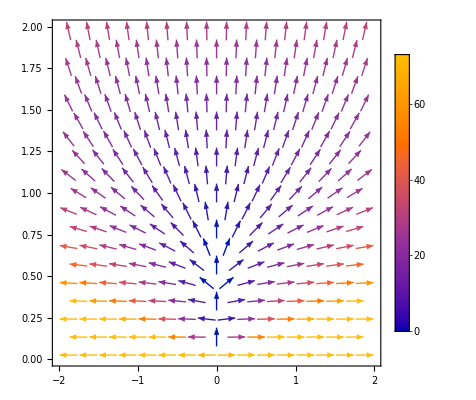

```mathematica
VectorPlot[{T0/H,H^2/2},{T0,-2,2},{H,0,2},PlotLegends->Automatic]
```